# Разработка алгоритма обнаружения движения в среде программирования Mathematica

Вадим Залива <lord@crocodile.org>

В данной статье мы рассмотрим пример использования среды Mathematica для быстрого прототипирования простого алгоритма определения движения. Кроме общих приемов работы с Mathematica, мы познакомим читателя с некоторыми понятиями из области machine vision и signal processing.

## Задача

Недавно перед нами стала задача разработать программу, которая позволяет использовать мобильный телефон (iPhone) в качестве системы сигнализации. Телефон при помощи видеокамеры наблюдает за помещением и, если обнаружено движение, подает звуковой сигнал, фотографирует движущийся объект и передает изображение в Интеренет. Ключевая часть этой программы − это алгоритм определения движения. Конечно, можно было бы его сразу написать на Objective-C и производить отладку на телефоне, но такой процесс был бы довольно трудоемким. Вместо этого мы решили использовать среду программирования Mathematica и, уже проверив и отладив в ней алгоритм, переписать его на Objective-C.

Пакет Mathematica - продукт фирмы Wolfram Research является мощным вычислительным инструметом, используемым академической и инженерной среде.  Работа обычно ведется в записных книжках - интерактвных документах содержащих формулы, графики, данные и текст. Они обычно сохряняются в файлах с расширением .nb.  Создаваемый код выполняется по мере его написания и результаты представляются сразу вместе с кодом. Это черезвычайно удобный режим для интерактивной работы. Более сложные функции можно оформить в виде модулей (файлов с расширрением .m) на которые можно ссылаться из записных книжек.

Пакет Mathematica умеет работать в видеокамерой, но поскольку нашей целью было быстрое прототипирование алгоритма, мы не воспользовались этой возможностью, а работали с записаным с готовым видеофайлом. Также, поскольку этот алгоритм планировалось в дальнейшем реализовывать на другом языке, мы старались применять простейшие базовые функции, а не использовать более мощные встроенные функции пакета. Так, например, мы не воспользовались стандартными функциями работы с изображениями для масштабирования кардров и перевода их в серое цветовое пространство в оттенках серого (greyscale).

Первая рабочая версия данного алогоритма, включая запись тестового видеоролика (созданная при помощи того же iPhone),  была разработана примерно за 2 часа. Это демонстрирует удобство пакета Mathematica для быстрого решения подобных задач. В дальнейшем аглортим был реализован и использован в программе iSentry для iPhone[1].

Для начала мы записали тестовый видеоролик, на котором производилась отладка алгоритма. Это 6-ти секундный ролик, на котром на столе под лампой стоит детская игрушка (динозавр). Через некоторое время в кадре появляется iPhone, брошенный на стол. Еще через некоторое время в кадре появляется рука, которая двигает игрушку. Ролик можно закачать тут [2].

## Алгоритм

### Работа с видео и картинками

Запустим пакет Mathematica, и создадим пустую записную книжку. Допустим, что ролик в файле с именем movement.mov находится в той же директории что и наша записная книжка. Теперь мы можем набрать нашу первую строку кода на Mathematica:

```mathematica
raw=Import[ToFileName[NotebookDirectory[],"movement.mov"], "Data"];
```

Давайте рассмотрим ее подробнее. Синтаксис пакета Mathematica использует  для указания аргументов функций квадратные, а не круглые скобки. Функция NotebookDirectory  возрашает полный путь директории, в которой расположена текущая записная книжка. Параметр ToFileName формирует абсолютный путь из директории и имени файла. Обычно функция Import сама пытается “угадать” формат файла, но, можно его указать явно. Для каждого поддерживаемого типа файлов она умеет загружать разные элементы. В данном случае нас интересуют данные в виде массивов чисел, что мы и указываем при помощи второго параметра “Data”. Результат присваивается переменной с именем raw. Точка с запятой в конце  подавляет показ результата непосредствено под этой строкой в процессе выполнения. Результатом будет список кадров.

Чтобы узнать количество кадров в  прочитанном файле, можно воспользоваться функцией Length. Результатом работы функции будет количество кадров (элементов списка) в переменной  nframes.

```mathematica
nframes=Length[raw]
```

196

В случае вложенных структур данных Length считает количество элементов на самом верхнем уровне. В данном случае получилось 196 кадров. Если же мы хотим необходимо получить все измерения (предполагая что у нас регулярная многомерная структура), можно воспользоваться функцией Dimensions:

```mathematica
Dimensions[raw]
```

{196,240,320,3}

Теперь рассмотрим подробнее, как представлены кадры. Базовая структура данных - это список. В данном случае у нас есть список из 196 элементов (кадров). Каждый кадр - это матрица размером 240 строк по 320 элементов каждая. В Mathematica (в отличие от языков типа R) нет специальной структуры данных для матриц, они тоже представлены как вложенные списки. Каждый элемент, представляет собой список из 3-х значений, соответствующих RGB-компонентам цветовой модели. Каждая компонента может принимать значения от 0 до 255. Чтобы узнать значение цвета первого пикселя в первой строке первого кадра достаточно написать выражение (поскольку квадратные скобки используются в нотации вызова функций, для доступа к элементам массивов используются двойные квадратные скобки):

```mathematica
raw[[1,1,1]]
```

{42,33,20}

В Mathematica есть встроенный тип данных Image, которым мы в данном примере будем пользоваться только для визуализации. Все что нам нужно знать - это то, что создать Image из матрицы значений пикселей (первый кадр) можно следующей командой:

```mathematica
Image[raw[[1]],"Byte"]
```

-Graphics-

### Перевод в серую шкалу

Для определения движения информация о цвете нам не нужна и нам поэтому будет гораздо проще работать не с цветной картинкой, представленной 3-мя компонентами а с картинкой изображением в серой шкале, представленной одним значением. Для перевода RGB в серую шкалу мы воспользуемся известной формулой:

```mathematica
I = 0.3*R + 0.59*G + 0.11*B;
```

Эта формула основана на чувствительности человеческого глаза к различным частям спектра [3]. Поскольку в нашем случае  картинки будет обрабатывать алгоритм, а не  человеческий глаз, точные значения не так важны, и поэтому можно было бы использовать 33% для каждого компонента.

Пребразование всех кадров серую шкалу выполняется следующей командой:

```mathematica
orig =Map[(#.{0.3,0.59,0.11})&,raw,{3}];
```

Давайте рассмотрим ее подробнее. Мы используем функцию Map которая применяет указанное выражение к каждому элементу структуры данных. В функциональных языках обычно эта функция определена для списков и применяет выражение к элементам списка первого уровня. В Mathematica она также позволяет работать с вложенными списками произвольной глубины. Функция Map имеет три параметра. Первый параметр это функция. Второй параметр это список произвольной вложенности. Третий, опциональный параметр указывает к каким уровням вложенности списка применять указанную функцию. В нашем случае его значение {3} обозначет что применять к элементам 3-тего уровня вложенности. Напомним, что в нашей структуре данных первый уровень это кадры, второй это строки кадра,  а третий это пиксели в строке. То есть функция будет применена к каждому пикселю, который будет ей передан как список из 3-х элементов. Поскольку у нас нет готовой определенной функции для перевода RGB в серую шкалу, мы первым параметром Map передаем то, что в Mathematica называется pure function, а в других языках известно как анонимная функция или лямбда-выражение. В нашем примере она определена при помощи оператора ‘&’. Выражение перед ‘&’ является телом функции. На формальные параметры можно ссылаться используя имена #1, #2, #3 и так далее. Для удобства #1 можно сокращать до #. Вычисления которые мы делаем довольно просты: список компонентов цвета для каждого пикселя мы поэлементно умножаем на коэффициенты {0.3,0.59,0.11} и суммируем (используя векторное произведение). Результатом работы всего выражения будет список кадров в котором каждый элемент представлен уже не тройкой RGB а одним значением оттенка серого цвета.

Image  также умеет работать с такими изображениями тоже, и мы можем визуализировать первый кадр чтобы взгялянуть на результат:

```mathematica
Image[orig[[1]],"Byte"]
```

-Graphics-

### Масштабирование

Оригинальные кадры имели размер 320x240 пикселей. Для нашей задачи даже такое довольно таки низкое разрешение излишне. Кроме того, поскольку окончательное приложение будет работать на мобильном телефоне, где процессорные ресурсы ограничены и использование CPU связано с расходом батарейки, имеет смысл смасштабировать кадры, по крайней мере, уменьшив в два раза по каждому измерению, что уменьшит количество пикселей в четыре раза. В принципе нам не обязательно масштабировать пропорционально, но для простоты мы будем использовать пропорциональное масштабирование, так что фактор маштабирования у нас будет один для обеих измерений:

```mathematica
scaleFactor = 2;
```

Процесс масштабирования картинки (с уменьшением размера) на фактор scaleFactor называется downsamping. Обычно этот процесс делается в 2 этапа:

1. Применение фильтра нижних частот (low-pass filter) для удовлетворения теоремы Котельникова (в англоязычной литературе известной как Nyquist–Shannon sampling theorem)

2. Уменьшение количества пикселей выбором элементов с шагом scaleFactor.

Рассмотрим эти шаги подробнее. Не вдаваясь в теорию информации, достаточно сказать что на шаге 1 мы применим так называемый усредняющий фильтр. Интуитивное определение этого фильтра доволно простое: каждая точка будет заменена на среднее значение ее окрестности с заданным радиусом. В более общем случае, определение значения точки через ее окрестность довольно частая операция в обработке изображений и обычно выражается через свертку. В функиональном анализе свертка двух функций f и g определяется как:

[f*g](x)= ∫_(-∞)^∞ f(u)g(x-u)ⅆu

Для 2-х мерных растровых изображений мы можем записать дискретную форму этой формулы.

F(x,y)= ∑_i ∑_j f(i,j)g(x-i,y-j)

В этой формуле f(x,y) это значения пикселей изображения до применения свертки. F(x,y) это функция, которая дает  значения после применения свертки. Собственно, свертка задается функцией g(x,y). Для большинства практических применений функция g опеределена на небольшом диапазоне значений (обычно в несколько пикселей). Ее удобно представлять как матрицу, которую иногда называют ядро свертки.

Применение операции свертки, заданной таким ядром к изображенииям очень хорошо распараллелирвается и часто выполняется при помощи GPU.

Теперь представьте, что мы возьмем матрицу размером (2*scaleFactor+1) × (2*scaleFactor+1). В нашем случае в ней будет (2*scaleFactor+1)^2 элементов. Установим каждый элемент этой матрицы значением 1/(2*scaleFactor+1)^2.  Такую матрицу можно получить, выполнив  следующюю команду:

```mathematica
meanKernel=BoxMatrix[scaleFactor]/((2*scaleFactor+1)^2);
MatrixForm[meanKernel]
```

(1/25 | 1/25 | 1/25 | 1/25 | 1/25
1/25 | 1/25 | 1/25 | 1/25 | 1/25
1/25 | 1/25 | 1/25 | 1/25 | 1/25
1/25 | 1/25 | 1/25 | 1/25 | 1/25
1/25 | 1/25 | 1/25 | 1/25 | 1/25)

Это и есть наше ядро свертки для усредняющего фильтра с радусом scaleFactor. Если его применить к каждому пикселю изображения,  то мы получим среднее значение из окрестности  25-ти соседних пикселей (включая текущий).

Функция ListConvolve позволяет применить ядро к списку значений. Количество измерений списка и ядра может быть произвольной, но должны совпадать. Дополнительный параметр уточняет, как обрабатывать значения около краев, когда применяемый фильтр выходит за границы данных. Детальное описание опций ListConvolve можно посмотреть в документации по Mathematica. Используя уже знакомую нам функцию Map,  можно применить mean фильтр ко всем кадрам:

```mathematica
origc=Map[ListConvolve[meanKernel,#,{-1,-1},0]& ,orig];
```

Как и ождалось, результирущая  сглаженная картинка выглядит “размытой”. Не зря mean фильтр еще называю сглаживающим фильтром.

```mathematica
Image[origc[[1]],"Byte"]
```

-Graphics-

Теперь можно выполнить второй шаг и выбрать пиксели с шагом scaleFactor. Выбор элементов из списка можно сделать при помощи функции Take. В нашем случае мы указываем ей два критерия выбора  - по одному на каждое измерение. Критерй задан в виде списка вида {начальное_значение, конечное_значение, шаг}.

```mathematica
origdim=Dimensions[orig]
```

{196,240,320}

```mathematica
bwm=Map[Take[#,{1,origdim[[2]],scaleFactor},{1,origdim[[3]],scaleFactor}]&,origc];
```

В результате  получаем массив кадров уменьшенного размера:

```mathematica
Dimensions[bwm]
```

{196,120,160}

Давайте посмотрим, что у нас получилось. На этот раз мы не просто визуализируем изображение одного из кадров, а применим функцию под названием Manipulate. Это один из очень удобных и мощных инструментов в Mathematica, который позволяет визулизировать данные, динамически изменяя значения параметров. Опять же мы не будем вдаваться во все возможности и способы использования этого механизма, а продемонстрируем простейший вариант, который очень уместен в нашем случае:

```mathematica
Manipulate[Image[bwm[[f]],"Byte"] ,{f,1,nframes,1}]
```

Первым параметром передается выражение. В  нашем случае оно преобразовывает кадр с номером f из списка bwm в формат Image. Заметьте, что в отличие от Map, это не функция, а просто фрагмент кода, и, соответсвенно, мы не используем оператор ‘&’. Второй параметр это список, состоящий из имени переменной, начального, конечного значений и шага. Функция Manipulate позволяет пользователю изменять значения переменной и при каждом изменении пересчитывает выражение с новыми значениями, показывая результат. Возможно изменять более одного значения, но в нашем случае номера кадра нам достаточно. Двигая движок f , пользователь может прокручивать получившиеся видео покадрово. Также можно перейти к произвольному кадру, введя его номер или включить механизм автоматической прокрутки (анимацию).

Мы законичили предварительную обработку данных и теперь готовы перейти собсвтенно к алгориму определения движения.

### Оценка количества движения

Как мы будем определять движение? Простейщий подход - смотреть насколько изменилось изображение между кадрами. Просто сравнивать кадр с предыдущим будет недостаточно, так как программа будет чувствительна к мелким вариациям освещения и цифровому “шуму” камеры. Более надежный подход сравнивать текущий кадр с усредненным значением нескольких предыдущих. Это также будет довольно легко реализовать при работе в режиме реального времени: накапливая несколько послдених кадров в специальном буфере и используя их для сравнения. Такое сглаживание кадра по нескольким предыдущим называется частным случаем каузального фильтра. Название подчеркивает, что его значение зависит только от текущего и предыдущих кардров но не от будущих.

Для начала определим функцию, которая берет несколько кадров и строит на основании их “средний” кадр. Определение довольно очевидное:

```mathematica
avgFrame[d_] := Total[d]/Length[d]
```

Список кадров указан формальным параметром d_. В Mathematica существует довольно мощный механизм выбора подходящей функции на основании типов и количества параметров. Формальные параметры задаются в виде patterns. Все что нужно знать на данном этапе, это то, что в определении функции имена формальных параметров должны содержать символ подчеркивания (“_”), а в теле функции на них нужно ссылаться без этого символа. Нашей функции avgFrame передается на вход список кардов в виде матриц. Функция Total их суммирует поэлементно. Получившуюся матрицу мы делим на количество кадров тем самым получив на выходе матрицу средних значений пикселей заданных кадров.

Теперь можно определить функцию, реализующую сглаживающий фильтр. На вход передаем список кадров и размер окна сглаживания (количесто кадров). На этот раз используем операцию Map не по самим кадрам, а по их индексам. Из исходного массива мы выбираем поднможество элеменов, используя двойные квадратные скобки (оператор Part). Диапазон выбираемых значений задается в формате от ;; до (оператор Span).

```mathematica
avgFilter[l_,w_]:= 
	Map[avgFrame[l[[Max[1,#-w];;#]]] &, Range[Length[l]]]
```

Теперь мы можем можно применить наш фильтр. Значение окна подбирается экспериментально в зависимости от желаемой “чувствительности” алгоритма и частоты получения кадров. Допустим, мы будем использовать значение 10. При частоте кадров 30 это соотвествует 1/3 секунды.

```mathematica
bwms=avgFilter[bwm,10];
```

Таким образом мы получили кадры, которые “сглажены” по времени. Если их визуализировать, то в местах, где нет движения, изображение мало отличается от оригинального,  а в местах, где наблюдается движение, движущиеся части немного размыты. Сам по себе этот промежуточный результат мало интересен. Более интересно взглянуть на разницу между несглаженым по времени кадром (bwm) и сглаженым (bwms).  На статических кадрах разницы не будет и результатом будет кадр с нулевыми значениями пикселей (черный). На кадрах, где присуствует движение мы увидим изменившуюся часть. Посмотрим на пару показательных кадров:

В кадре номер 50 телефон движется “въезжает” в кадр:

```mathematica
Image[bwm[[50]]-bwms[[50]],"Byte"] // ImageAdjust
```

-Graphics-

В кадре 139 мы видим движущуся руку:

```mathematica
Image[bwm[[139]]-bwms[[139]],"Byte"] // ImageAdjust
```

-Graphics-

Кроме знакомой функции Image, тут использована еще функция ImageAdjust. Эта функция масштабирует значения пикселей, чтобы они были в диапазоне от 0 до 1, что позволяет  лучше рассмотреть темные кадры. Кроме того, тут использован оператор “//”. Это постфикс-нотация применения функций. Запись F[x] // G эквивалентна G[F[x]].

Ну и как обычно,  можно воспользоваться функцией Manipulate, чтобы посмотреть на произвольные кадры, интерактивно прокручивая список.

```mathematica
Manipulate[ImageAdjust[Image[bwm[[f]]-bwms[[f]], "Byte"]],{f,1,nframes,1}]
```

Попробуем представить объем изменений в виде одного числа. Количество движения в указаном кадре кореллирует с тем, насколько текущий кадр (из списка bwm) отличается от усредненного значения нескольких предыдущих (из списка bwms). Оценить разницу этих двух кадров удобнее всего с помощью среднеквадратичного отклонения разницы соотвествующих пикселей поделенное на среднее значение пикселя в текущем кадре:

CV(RMSD(x,y))= (RMSD(x,y))/(x̄)=(√(1/n∑_(i=1)^n (x_i-y_i)^2))/(x̄)

На Mathematica это можно выразить вот так:

```mathematica
errs = Map[RootMeanSquare[Flatten[bwm[[#]]-bwms[[#]]]] / Mean[Flatten[bwm[[#]]]]&, Range[nframes]];
```

Заметим, что мы уменьшаем размерность данных при вызове функции Mean, используя функцию Flatten. В противном случае, мы получим не одно среднее значение по всем пикселям кадра, а вектор средних значений столбцов.

В переменной errs у нас должен был получится список значений, отражающих количество движения в каждом кадре. Попробуем нарисовать график  этих значений. Команда Needs позволяет подгружать внешние модули. В данном случае мы используем модуль PlotLegends, который позволяет показывать легенду на графике.

```mathematica
Needs["PlotLegends`"]
```

Собственно рисование графика выполняется функцией ListLinePlot.

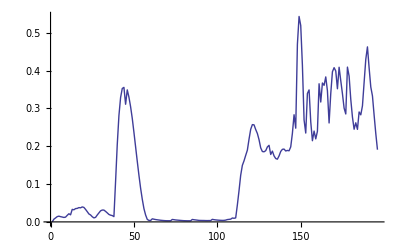

```mathematica
ListLinePlot[errs, PlotLegend ->{"движение"},LegendPosition->{0.8,-0.8}]
```

Можно заметить два видимых всплеска активности: первый в диапазоне кадров 40-60 а второй начиная с кадра 110.

### Сглаживание сигнала при помощи линейной регрессии

Используя получившийся график, можно уже попробовать фиксировать движение, но для начала имеет смысл его немного сгладить, чтобы уменьшить влияние случайного шума. Сглаживать будем опять же при помоши causal filter. На этот раз применим для сглаживания линейную регрессию. Идея доовльно проста. В качестве сглаженного значения точки будем использовать ее регрессию в зависимости от предыдущих нескольких точек. Для этого постараемся найти прямую, которая ближе всего описывает предудыщие точки. Искомое значение - точка на этой прямой с абсциссой, соотвествующей текущему (последнему) значению.

Рассмотрим пример, взяв произвольный диапазон значений из списке errs. Допустим что диазон задан начальным и конечным значеним f и t.

```mathematica
f=3;t=13;
```

Сформируем список точек, заданных парой координат. Первая координата - порядковый номер. Вторая - собственно значение. Список первых координат легко получить при помощи функции Range, список вторых - используя оператор Span (;;) из списка errs. Их можно поместить в список из двух элеменов, используя фигурные скобки. Если рассматривать получившуюся структуру как матрицу, то ее размерность будет 2 строки и 11 столбцов. Транспонировав ее при помощи функции Transpose, мы получим нужный нам список пар:

```mathematica
fdata=Transpose[{Range[f,t],errs[[f;;t]]}]
```

{{3,0.0104027},{4,0.0139062},{5,0.0151486},{6,0.0138507},{7,0.012893},{8,0.0117535},{9,0.0125816},{10,0.0172805},{11,0.0215209},{12,0.0187361},{13,0.0330796}}

Применим линейную регрессию. Для начала мы это сделаем при помощи функции Fit. Первым параметром передадим пары значений. Второй параметр задает тип многочлена коэффициенты, которого собираемся вычислить Третий -  перечисляет переменные многочлена. Результатом является выражение, которое использует эти переменные.

```mathematica
fit=Fit[fdata,{1,x},x]
```

0.00495072+0.00143972 x

Теперь можно применить это выражение, используя операцию подстановки (/.). Эта операция применяет указанные правила подстановки к заданному выражению. Например, можно посчитать последню точку:

```mathematica
lastt={t,fit /. x-> t}
```

{13,0.0236671}

Итак, мы можем отобразить наш пример:

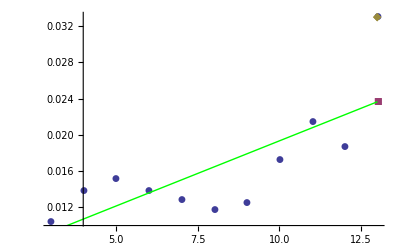

```mathematica
Show[{ListPlot[{fdata,{lastt},{Last[fdata]}},PlotMarkers-> Automatic],
Plot[fit ,{x,f,t},PlotStyle->Green]
	
}]
```

Синие точки - исходные данные. Зеленая линия - прямая, которой мы их апроксимировали. Коричневая точка - несглаженное значение. Красная - сглаженное. Мы не будем рассматривать подробно функции Plot, ListPlot и Show, лишь обратим внимание, что Show используется для отображения нескольких графиков используя общую систему координат.

Оформим этот механизм в виде функции. Сначала определим функцию lmsmoothPoint, которая берет список значений равномерно распределенных точек и на основании них вычисляет сглаженное значение последней. Отметим, что здесь используется несглаженное значение как часть набора данных для регрессии. Мы допускаем, что в переданном нам наборе данных могут быть неопределенные значения. Мы их просто опускаем, используя функцию Select совместно с предикатом NumberQ, который возрщает FALSE для нечисловых значений как, например,  иногда используемого в Mathematica символа Indeterminate. Если после отбрасывания неопределенных значений у нас останется недостаточно данных для линейной регресии (меньше 2-х точек), то функция вернет неопределенное значение:

```mathematica
lmsmoothPoint[d_] := Module[{data,rdata},
	data = Transpose[{Range[Length[d]],d}];
	rdata =Select[data,NumberQ[N[#[[2]]]]&];
	If[Length[rdata]<2,
		Last[d],
		Fit[rdata,{1,x},x] /. x-> Length[d]
	]
]
```

Следующим шгом можно определить функцию, которая берет набор данных и размер окна сглаживания и применяет сглаживание при помощи линейной регресии:

```mathematica
lmsmooth[l_,w_]:= 
	Map[lmsmoothPoint[l[[Max[1,#-w];;#]]] &, Range[Length[l]]]
```

А теперь применим ее к нашим данным и нарисуем сглаженное и несглаженное значения:

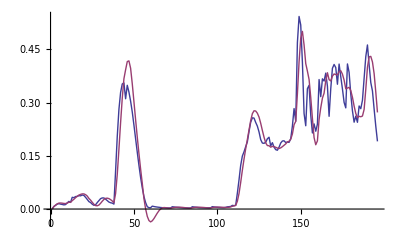

```mathematica
serrs=lmsmooth[errs,10];
ListLinePlot[{errs,serrs},PlotLegend ->{"движение","сглаженное"},LegendPosition->{0.8,-0.8}]
```

### Определение движения

Последний шаг - собственно определение наличия движения в виде логического значения да/нет. Мы будем использовать пороговое значение, подстраиваемое пользователем. Диапазон этого значения будет [0..1]. Один из способов получить такие бинарные значения в зависимости от того больше элемент списка порога или нет,  это отнять пороговое значение от элементов списка и применить к ним функцию UnitStep. Эта функция возращает 0 для значений меньше 0 и 1 для остальных.

```mathematica
motionThreshold=0.05;
motionFlag=UnitStep[serrs-motionThreshold]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Теперь можно визуализировать окончательный результат работы нашего алгоритма:

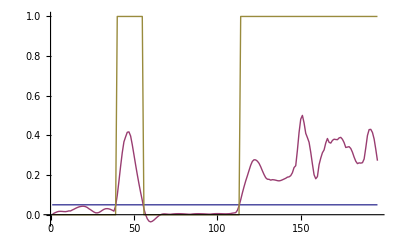

```mathematica
ListLinePlot[{Table[motionThreshold,{nframes}],serrs,motionFlag},
PlotLegend ->{"порог","движение","срабатывание"},LegendPosition->{0.8,-0.8}
]
```

## Заключение

Мы не ставили задачей обучить вас языку Mathematica. Мы умышленно тривиализировали многие понятия и не вдавались в детали внутреннего представления функций и данных в Mathematica. Нашей целью было показать стиль работы с этим пакетом в исследовательской работе на примере разработки этого несложного алгоритма. Надеемся, что заинтересованый читатель самостоятельно сможет изучить множество других возможностей этого пакета, используя материалы перечисленные в приведенном ниже списке литературы.

Алгоритм который мы разработали тоже был упрощен в учебных целях. В тоже время, даже в таком виде он вполне работоспособный.

Список литературы

1. iSentry. http://itunes.apple.com/us/app/isentry/id396777365

2. Тестовый ролик http://www.crocodile.org/lord/MotionDetection/movement.mov

3. http://en.wikipedia.org/wiki/Grey_scale